# Lab 5 - Grapefruit

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

```mathematica
v0test = 10
```

10

```mathematica
thetaMax = NMaximize[{v0test *Cos[th] *t, v0test*Sin[th]*t - .5 * 9.8 * t^2 ==0 ,t≥0},{th,t}][[2,1,2]]
```

0.785396

```mathematica
N[Pi/4]
```

0.785398

To show the graphs easily, we will paramiterize the functions and remove t. Let (x0,y0) = (0,0)

```mathematica
yX[x_,v0_,th_] := v0*Sin[th]*x/(v0 * Cos[th]) - 1/2 * 9.8 * (x/(v0 * Cos[th]))^2
```

Optimal firing angle is Pi/4. To reach a distance of 1000m, we need:

```mathematica
optV = Solve[yX[1000,v0,Pi/4]==0 && v0 > 0, {v0} ][[1,1,2]]
```

98.9949

```mathematica
xOpt = optV*Cos[Pi/4]
```

70.

```mathematica
yOpt = optV*Sin[Pi/4]
```

70.

```mathematica
d[x0_,v0_,t_, th_] := x0 + v0* Cos[th] * t
```

```mathematica
h[y0_, v0_, t_, th_] := y0 + v0 * Sin[th]*t - 1/2*9.8*t^2
```

Flight distance in the abscence of drag is only dependent on the x component of the velocity, which is v0 times the cosine of the firing angle, and the time of flight, which is dependent on the y components v0 times sine of firing angle.

```mathematica
thetas = Table[th, {th, 0, Pi/2 - Pi/36, Pi/36}]
```

{0,π/36,π/18,π/12,π/9,(5 π)/36,π/6,(7 π)/36,(2 π)/9,π/4,(5 π)/18,(11 π)/36,π/3,(13 π)/36,(7 π)/18,(5 π)/12,(4 π)/9,(17 π)/36}

```mathematica
data =Map[Function[th,yX[x,optV,th]], thetas];
```

```mathematica
ops = Table[Solve[optV * Sin[thetas[[i]]]*t -.5*9.8 * t^2 == 0 && t >= 0,t], {i, Length[thetas]}]
```

{{{t→0.},{t→0.},{t→0.},{t→0.}},{{t→0.},{t→0.},{t→1.76081}},{{t→0.},{t→0.},{t→3.50822}},{{t→0.},{t→0.},{t→5.22893}},{{t→0.},{t→0.},{t→6.90985}},{{t→0.},{t→0.},{t→8.53818}},{{t→0.},{t→0.},{t→10.1015}},{{t→0.},{t→0.},{t→11.588}},{{t→0.},{t→0.},{t→12.9863}},{{t→0.},{t→0.},{t→14.2857}},{{t→0.},{t→0.},{t→15.4764}},{{t→0.},{t→0.},{t→16.5494}},{{t→0.},{t→0.},{t→17.4964}},{{t→0.},{t→0.},{t→18.3102}},{{t→0.},{t→0.},{t→18.9847}},{{t→0.},{t→0.},{t→19.5146}},{{t→0.},{t→0.},{t→19.8961}},{{t→0.},{t→0.},{t→20.1262}}}

```mathematica
ops = Map[Function[t,t[[3,1,2]]],ops]
```

{0.,1.76081,3.50822,5.22893,6.90985,8.53818,10.1015,11.588,12.9863,14.2857,15.4764,16.5494,17.4964,18.3102,18.9847,19.5146,19.8961,20.1262}

```mathematica
ops = ops / Max[ops]
```

{0.,0.0874887,0.174311,0.259808,0.343327,0.424233,0.50191,0.575767,0.645243,0.709808,0.768971,0.822281,0.869333,0.90977,0.943282,0.969616,0.98857,1.}

```mathematica
ops = Map[Opacity,ops]
```

{Opacity[0.],Opacity[0.0874887],Opacity[0.174311],Opacity[0.259808],Opacity[0.343327],Opacity[0.424233],Opacity[0.50191],Opacity[0.575767],Opacity[0.645243],Opacity[0.709808],Opacity[0.768971],Opacity[0.822281],Opacity[0.869333],Opacity[0.90977],Opacity[0.943282],Opacity[0.969616],Opacity[0.98857],Opacity[1.]}

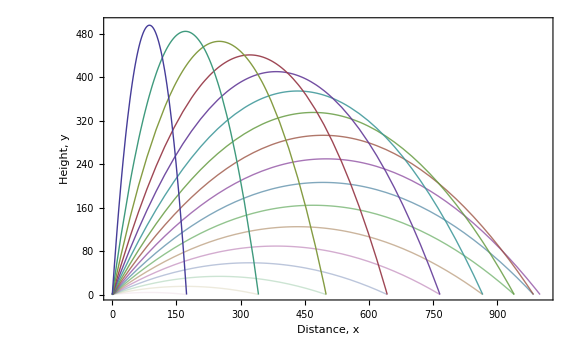

```mathematica
graph = Plot[data, {x, 0, 1010}, PlotStyle->ops,PlotRange->{0,500},Frame -> True, FrameLabel->{{"Height, y", ""},{"Distance, x", "Flight Trajectories"}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["trajectories.png", graph]
```

trajectories.png

Numerical Integration of DiffEQs:

```mathematica
eqs = {x''[t]==0,y''[t]==-9.8}
```

{x''[t]==0,y''[t]==-9.8}

```mathematica
ini={x[0]==0,y[0]==0,x'[0]==70,y'[0]==70}
```

{x[0]==0,y[0]==0,x'[0]==70,y'[0]==70}

```mathematica
rules = NDSolve[Join[eqs, ini],{x,y},{t,0,20}][[1]]
```

{x→InterpolatingFunction[{{0.,20.}},<>],y→InterpolatingFunction[{{0.,20.}},<>]}

```mathematica
xx[t_] := x[t] /.rules
```

```mathematica
yy[t_] := y[t] /. rules
```

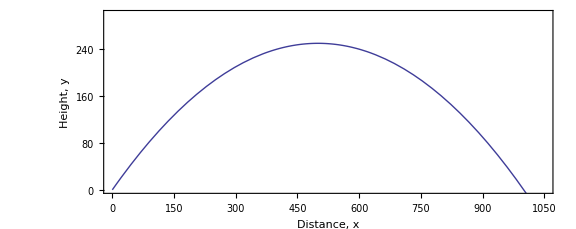

```mathematica
graph = ParametricPlot[{xx[t],yy[t]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,300}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Optimal Flight Trajectory"}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["trajectory.png", graph]
```

trajectory.png

With Drag

```mathematica
m = .5
```

0.5

```mathematica
r = .05
```

0.05

```mathematica
FDrag[v_]:= -.5 * 1.3*r^2*v^2
```

```mathematica
dragOpt = FDrag[optV]
```

-15.925

```mathematica
eqsD = {x''[t]==-Abs[FDrag[Sqrt[x'[t]^2 +y'[t]^2]]]*x'[t]/(m*Sqrt[x'[t]^2 +y'[t]^2]),y''[t]==-9.8-Abs[FDrag[Sqrt[x'[t]^2 +y'[t]^2]]]*y'[t]/(m *Sqrt[x'[t]^2 +y'[t]^2])}
```

{x''[t]==-(0.00325 Abs[x'[t]^2+y'[t]^2] x'[t])/(√(x'[t]^2+y'[t]^2)),y''[t]==-9.8-(0.00325 Abs[x'[t]^2+y'[t]^2] y'[t])/(√(x'[t]^2+y'[t]^2))}

```mathematica
iniD={x[0]==0,y[0]==0,x'[0]==70,y'[0]==70}
```

{x[0]==0,y[0]==0,x'[0]==70,y'[0]==70}

```mathematica
rulesD = NDSolve[Join[eqsD, iniD],{x,y},{t,0,20}][[1]]
```

{x→InterpolatingFunction[{{0.,20.}},<>],y→InterpolatingFunction[{{0.,20.}},<>]}

```mathematica
xx[t_] := x[t] /.rulesD
```

```mathematica
yy[t_] := y[t] /. rulesD
```

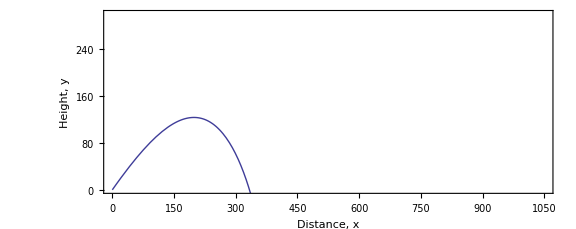

```mathematica
graph = ParametricPlot[{xx[t],yy[t]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,300}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Optimal Flight (without Drag) Trajectory in the Presence of Drag"}}, ImageSize-> Large, LabelStyle -> Larger ]
```

We get nowhere close to the 1000m target, instead falling to the ground at about 330m.

```mathematica
Export["drag.png", graph]
```

drag.png

Guess and Check (change the initial Conditions)

```mathematica
iniD={x[0]==0,y[0]==0,x'[0]==vX,y'[0]==vY}
```

{x[0]==0,y[0]==0,x'[0]==vX,y'[0]==vY}

```mathematica
V[th_, v_] :={vX =  Cos[th]*v, vY = Sin[th]*v}
```

```mathematica
v0 = 800
```

800

```mathematica
th0 = Pi/4
```

π/4

```mathematica
V[th0,v0]
```

{400 √2,400 √2}

```mathematica
rulesD = NDSolve[Join[eqsD, iniD],{x,y},{t,0,75}][[1]]
```

{x→InterpolatingFunction[{{0.,75.}},<>],y→InterpolatingFunction[{{0.,75.}},<>]}

```mathematica
xx[t_] := x[t] /.rulesD
```

```mathematica
yy[t_] := y[t] /. rulesD
```

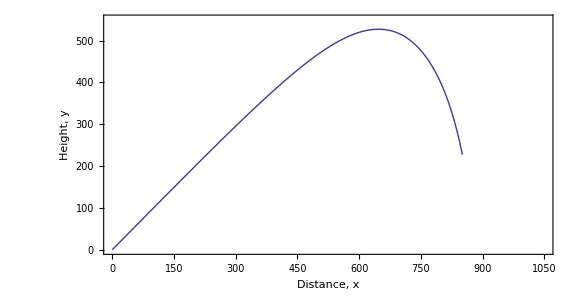

```mathematica
graph = ParametricPlot[{xx[t],yy[t]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,550}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Trajectory with Drag v0 = "  <> ToString[v0]  <>" theta = " <>  ToString[th0,InputForm]}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["dragGuess1.png", graph]
```

dragGuess1.png

```mathematica
v0 = 800
```

800

```mathematica
th0 = Pi/8
```

π/8

```mathematica
V[th0,v0]
```

{800 Cos[π/8],800 Sin[π/8]}

```mathematica
rulesD = NDSolve[Join[eqsD, iniD],{x,y},{t,0,75}][[1]]
```

{x→InterpolatingFunction[{{0.,75.}},<>],y→InterpolatingFunction[{{0.,75.}},<>]}

```mathematica
xx[t_] := x[t] /.rulesD
```

```mathematica
yy[t_] := y[t] /. rulesD
```

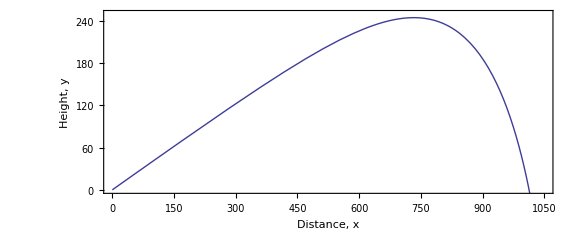

```mathematica
graph = ParametricPlot[{xx[t],yy[t]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,250}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Trajectory with Drag v0 = "  <> ToString[v0]  <>" theta = " <>  ToString[th0,InputForm]}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["dragGuess2.png", graph]
```

dragGuess2.png

```mathematica
v0 = 780
```

780

```mathematica
th0 = Pi /9
```

π/9

```mathematica
V[th0,v0]
```

{780 Cos[π/9],780 Sin[π/9]}

```mathematica
rulesD = NDSolve[Join[eqsD, iniD],{x,y},{t,0,75}][[1]]
```

{x→InterpolatingFunction[{{0.,75.}},<>],y→InterpolatingFunction[{{0.,75.}},<>]}

```mathematica
xx[t_] := x[t] /.rulesD
```

```mathematica
yy[t_] := y[t] /. rulesD
```

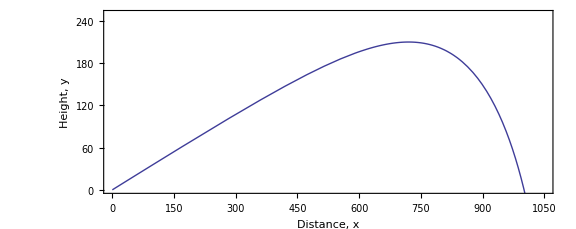

```mathematica
graph = ParametricPlot[{xx[t],yy[t]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,250}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Trajectory with Drag v0 = "  <> ToString[v0]  <>" theta = " <>  ToString[th0,InputForm]}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["dragGuess3.png", graph]
```

dragGuess3.png

```mathematica
initD[th_] := {x[0]==0,y[0]==0,x'[0]==v0*Cos[th],y'[0]==v0*Sin[th]}
```

```mathematica
initDs = Map[initD,thetas];
```

```mathematica
conds =Map[Function[x,Join[eqsD, x]], initDs];
```

```mathematica
rulesDs = Map[Function[c,NDSolve[c,{x,y},{t,0,200}][[1]]],conds];
```

```mathematica
xxs[t_] := Table[x[t] /.rulesDs[[i]],{i,Length[rulesDs]}]
```

```mathematica
yys[t_] := Table[y[t] /.rulesDs[[i]],{i,Length[rulesDs]}]
```

```mathematica
paraPlot = Transpose[{xxs[t],yys[t]}];
```

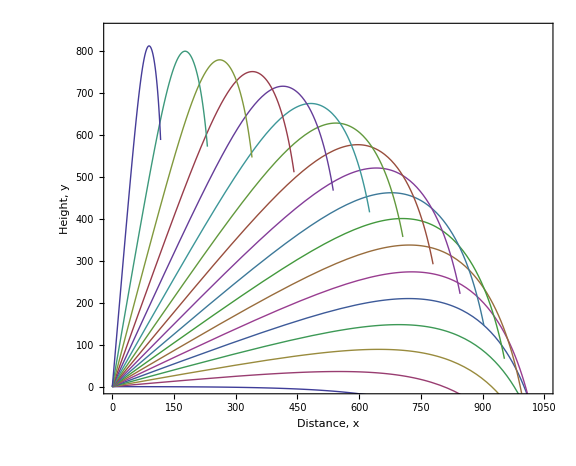

```mathematica
graph = ParametricPlot[paraPlot,{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,850}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Trajectory with Drag, v0 = " <> ToString[v0]}}, ImageSize-> Large, LabelStyle -> Larger ]
```

```mathematica
Export["dragTrajectories.png", graph]
```

dragTrajectories.png

```mathematica
thetas[[5;;7]]
```

{π/9,(5 π)/36,π/6}

```mathematica
closePlots = paraPlot[[5;;7]];
```

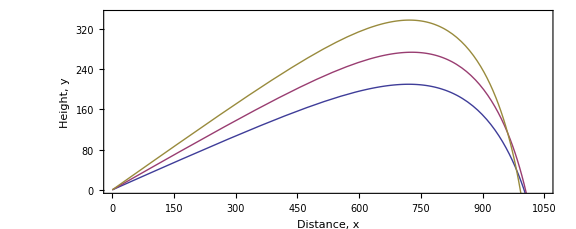

```mathematica
graph = ParametricPlot[{closePlots[[1]],closePlots[[2]],closePlots[[3]]},{t,0,16},Frame -> True, PlotRange->{{0,1050},{0,350}},FrameLabel->{{"Height, y", ""},{"Distance, x", "Trajectory with Drag, v0 = " <> ToString[v0]}}, ImageSize-> Large, LabelStyle -> Larger,PlotLegend->{Style["θ=Pi/9",15],Style["θ=5Pi/36",15],Style["θ=Pi/6",15]},LegendPosition->{.5,-.4},LegendSize->.4, PlotStyle->Thick]
```

```mathematica
Export["closeDrag.png", graph]
```

closeDrag.png

Better Methods